```mathematica
noErrors[x_]:=If[Head@x===Around,x[[1]],x];
relError[x_]:=If[Head@x===Around,x[[2]]/x[[1]],0];
```

```mathematica
energies={1,5,10,20,30,40,60,80,100,130,160,200,250,300,400,500,600,700,800,900,1000}; (*MeV*)
NbOfNeutrons={Around[0,0],Around[0,0],Around[0,0],Around[0.00419,0.00021116],Around[0.01373,0.000418649],Around[0.02191,0.000538625],Around[0.0390966,0.000771865],Around[0.0534749,0.000913252],Around[0.0687576,0.00104187],Around[0.0931065,0.00123096],Around[0.113663,0.00133698],Around[0.138203,0.00147519],Around[0.172006,0.0016357],Around[0.205119,0.00178519],Around[0.271099,0.00204833],Around[0.340685,0.0022764],Around[0.401409,0.00244442],Around[0.457938,0.00259656],Around[0.530084,0.00277888],Around[0.584798,0.00289441],Around[0.644229,0.00300957]};
NbOfNeutronsHP={Around[0,0],Around[0,0],Around[0,0],Around[0.00427,0.000211144],Around[0.01348,0.00041573],Around[0.02238,0.000549751],Around[0.0394059,0.000779513],Around[0.0541411,0.000930706],Around[0.0704007,0.00106751],Around[0.0905035,0.00119796],Around[0.112325,0.00133902],Around[0.138759,0.00148316],Around[0.172355,0.00164668],Around[0.208491,0.00180238],Around[0.276708,0.00207325],Around[0.34039,0.00227841],Around[0.405776,0.00247129],Around[0.46298,0.00261904],Around[0.528563,0.00276874],Around[0.589357,0.00290005],Around[0.644549,0.00301267]};
```

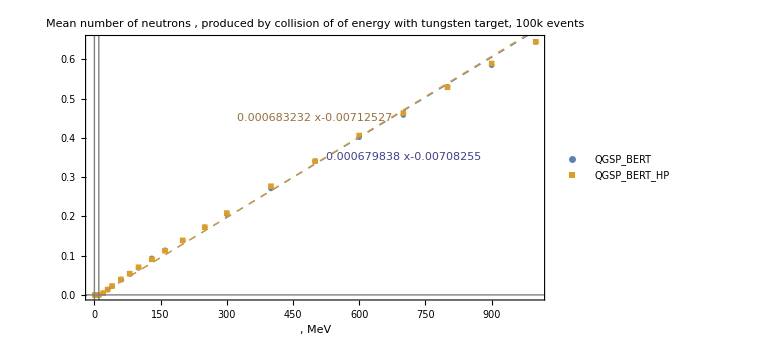

```mathematica
data=Table[{energies[[i]],NbOfNeutrons[[i]]},{i,1,Length@NbOfNeutrons}];
dataHP=Table[{energies[[i]],NbOfNeutronsHP[[i]]},{i,1,Length@NbOfNeutronsHP}];
fit=LinearModelFit[data[[4;;]],{1,x},x];
fitHP=LinearModelFit[dataHP[[4;;]],{1,x},x];
Show[
ListPlot[{data,dataHP},PlotRange->Full,FrameTicks -> {{Automatic,Automatic}, {Automatic, None}}, 
PlotLabel ->  "Mean number of neutrons , produced by collision\n of  of energy  with  tungsten target, 100k events",  FrameLabel -> {",  MeV",""}, Frame -> True,PlotLegends->{"QGSP_BERT","QGSP_BERT_HP"}, 
 LabelStyle -> {FontSize -> 18, FontFamily -> "Times"},PlotMarkers->{Automatic,Scaled[0.01]},AxesOrigin->{0,0},Axes->True,Epilog->{{Gray,Thin,InfiniteLine[{0,0},{0,1}],InfiniteLine[{0,0},{1,0}],InfiniteLine[{10,0},{0,1}]},{ColorData[1,1],Text[fit[x],{700,0.35}]},{ColorData[1,7],Text[fitHP[x],{500,0.45}]}},ImageSize->Large],
Plot[{fit[x],fitHP[x]},{x,0,1000},PlotStyle->Directive[Thickness[0.0015],Dashed]]
]
Export["C:\\Users\\mrgeb\\OneDrive\\Documents\\вольфрам стафф\\G4SuperEpicResult.pdf",%];
```

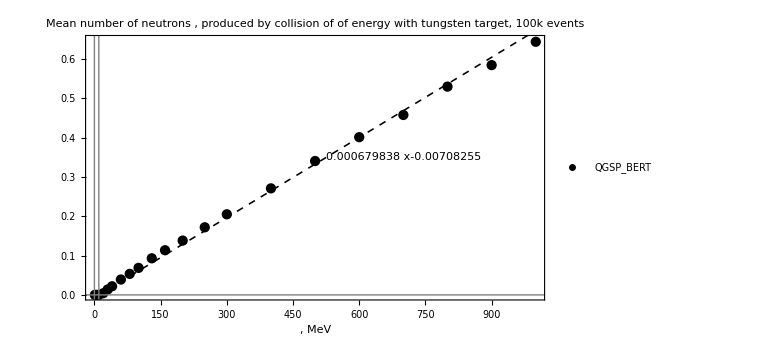

```mathematica
Show[
ListPlot[{data},PlotRange->Full,FrameTicks -> {{Automatic,Automatic}, {Automatic, None}}, 
PlotLabel ->  "Mean number of neutrons , produced by collision\n of  of energy  with  tungsten target, 100k events",  FrameLabel -> {",  MeV",""}, Frame -> True,PlotLegends->{"QGSP_BERT"},PlotStyle->Black, 
 LabelStyle -> {FontSize -> 18, FontFamily -> "Times"},Epilog->{{Gray,Thin,InfiniteLine[{0,0},{0,1}],InfiniteLine[{0,0},{1,0}],InfiniteLine[{10,0},{0,1}]},{Black,Text[fit[x],{700,0.35}]}},ImageSize->Large],
Plot[{fit[x]},{x,0,1000},PlotStyle->Directive[Black,Thickness[0.002],Dashed]]
]
```

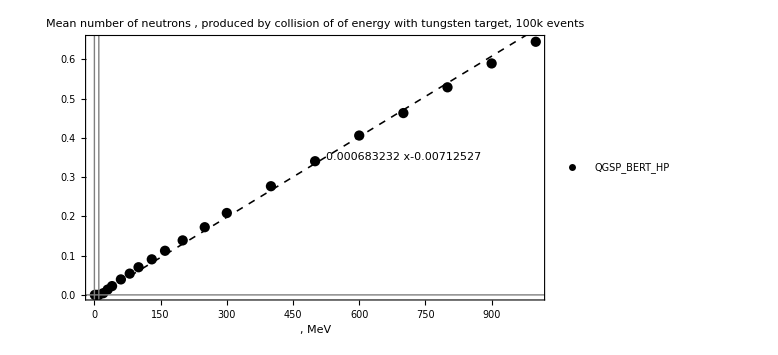

```mathematica
Show[
ListPlot[{dataHP},PlotRange->Full,FrameTicks -> {{Automatic,Automatic}, {Automatic, None}}, 
PlotLabel ->  "Mean number of neutrons , produced by collision\n of  of energy  with  tungsten target, 100k events",  FrameLabel -> {",  MeV",""}, Frame -> True,PlotLegends->{"QGSP_BERT_HP"},PlotStyle->Black, 
 LabelStyle -> {FontSize -> 18, FontFamily -> "Times"},Epilog->{{Gray,Thin,InfiniteLine[{0,0},{0,1}],InfiniteLine[{0,0},{1,0}],InfiniteLine[{10,0},{0,1}]},{Black,Text[fitHP[x],{700,0.35}]}},ImageSize->Large],
Plot[{fitHP[x]},{x,0,1000},PlotStyle->Directive[Black,Thickness[0.002],Dashed]]
]
```

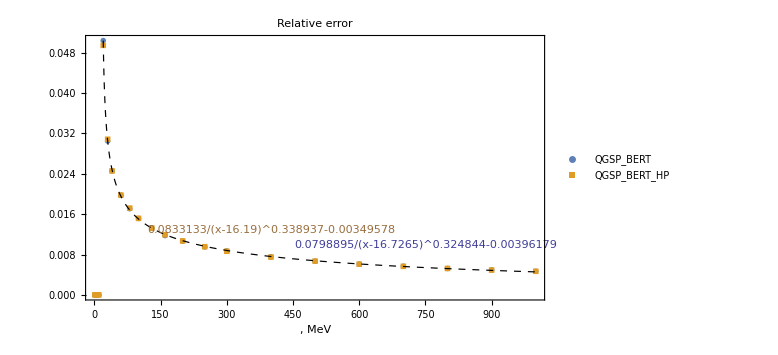

```mathematica
dataErr=Table[{energies[[i]],relError[NbOfNeutrons[[i]]]},{i,1,Length@NbOfNeutrons}];
fitErr=NonlinearModelFit[dataErr[[4;;]],A + a/((x-f^2)^α),{{A,0},{a,1},{f,3},{α,1}},x];
dataHPErr=Table[{energies[[i]],relError[NbOfNeutronsHP[[i]]]},{i,1,Length@NbOfNeutronsHP}];
fitHPErr=NonlinearModelFit[dataHPErr[[4;;]],A + a/((x-f^2)^α),{{A,0},{a,1},{f,3},{α,1}},x];
Show[
ListPlot[{dataErr,dataHPErr},FrameTicks -> {{Automatic,Automatic}, {Automatic, None}}, 
 PlotLabel ->  "Relative error ",  FrameLabel -> {",  MeV",""}, Frame -> True,PlotLegends->{"QGSP_BERT","QGSP_BERT_HP"}, 
 LabelStyle -> {FontSize -> 18, FontFamily -> "Times"},PlotMarkers->{Automatic,Scaled[0.02]},Epilog->{{ColorData[1,1],Text[fitErr[x],{750,0.01}]},{ColorData[1,7],Text[fitHPErr[x],{400,0.013}]}},ImageSize->Large],
Plot[fitErr[x],{x,1,1000},PlotStyle->Directive[Thickness[0.0015],Dashed,Black],PlotRange->Full]
]
```

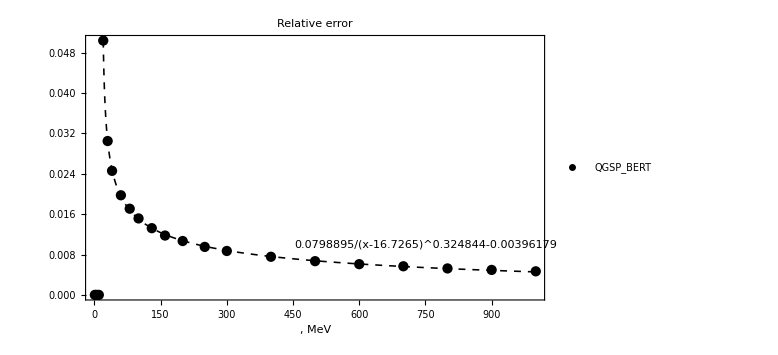

```mathematica
Show[
ListPlot[{dataErr},FrameTicks -> {{Automatic,Automatic}, {Automatic, None}}, 
 PlotLabel ->  "Relative error ",  FrameLabel -> {",  MeV",""}, Frame -> True,PlotLegends->{"QGSP_BERT"}, PlotStyle->Black,
 LabelStyle -> {FontSize -> 18, FontFamily -> "Times"},Epilog->{Black,Text[fitErr[x],{750,0.01}]},ImageSize->Large],
Plot[fitErr[x],{x,1,1000},PlotStyle->Directive[Thickness[0.002],Dashed,Black],PlotRange->Full]
]
```

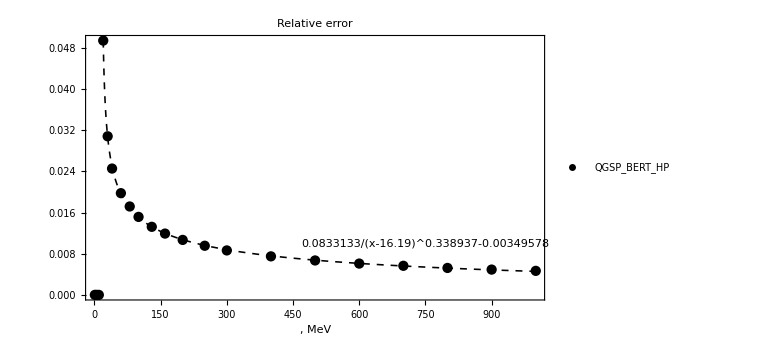

```mathematica
Show[
ListPlot[{dataHPErr},FrameTicks -> {{Automatic,Automatic}, {Automatic, None}}, 
 PlotLabel ->  "Relative error ",  FrameLabel -> {",  MeV",""}, Frame -> True,PlotLegends->{"QGSP_BERT_HP"}, PlotStyle->Black,
 LabelStyle -> {FontSize -> 18, FontFamily -> "Times"},Epilog->{Black,Text[fitHPErr[x],{750,0.01}]},ImageSize->Large],
Plot[fitHPErr[x],{x,1,1000},PlotStyle->Directive[Thickness[0.002],Dashed,Black],PlotRange->Full]
]
```